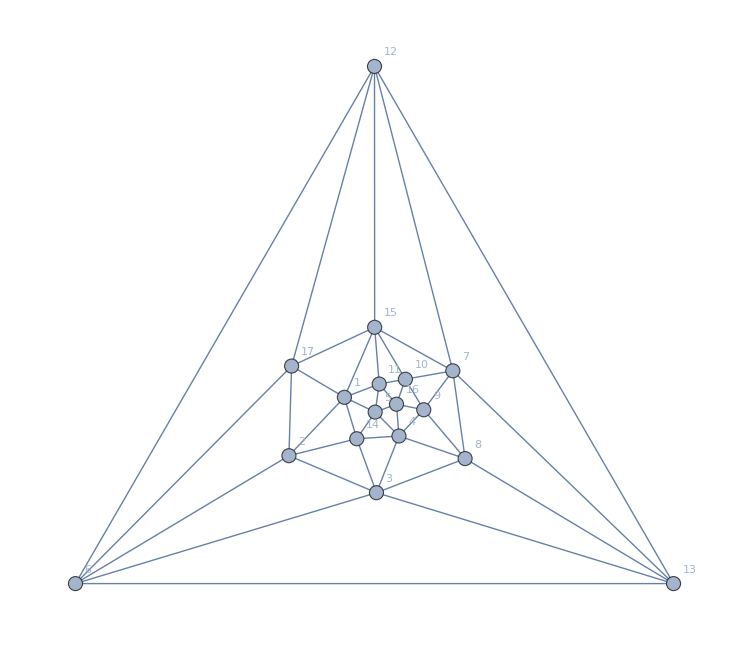

```mathematica
plantri8
```

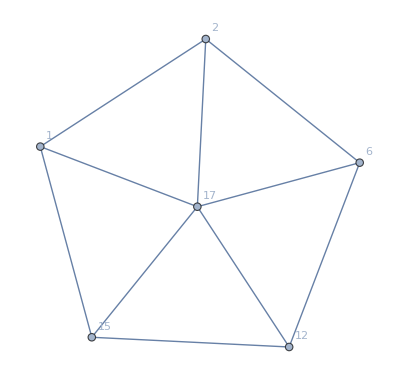

```mathematica
left=Subgraph[plantri8,{12,15,1,2,6,17},VertexLabels->"Name"]
```

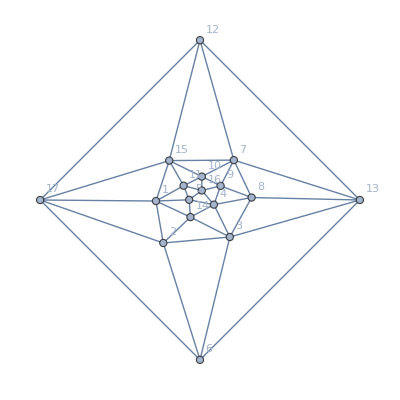

```mathematica
right=EdgeDelete[plantri8,6<->12]
```

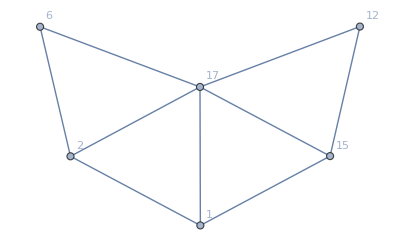

```mathematica
middle=EdgeDelete[Subgraph[plantri8,{12,15,1,2,6,17},VertexLabels->"Name"],6<->12]
```

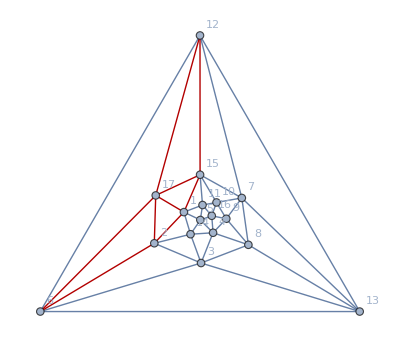

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[middle]]
```

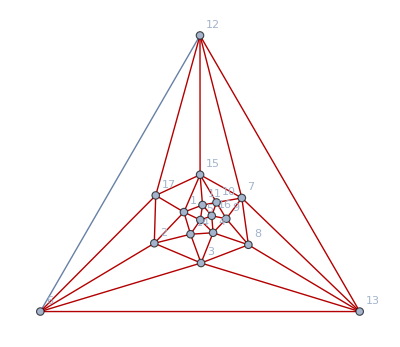

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[right]]
```

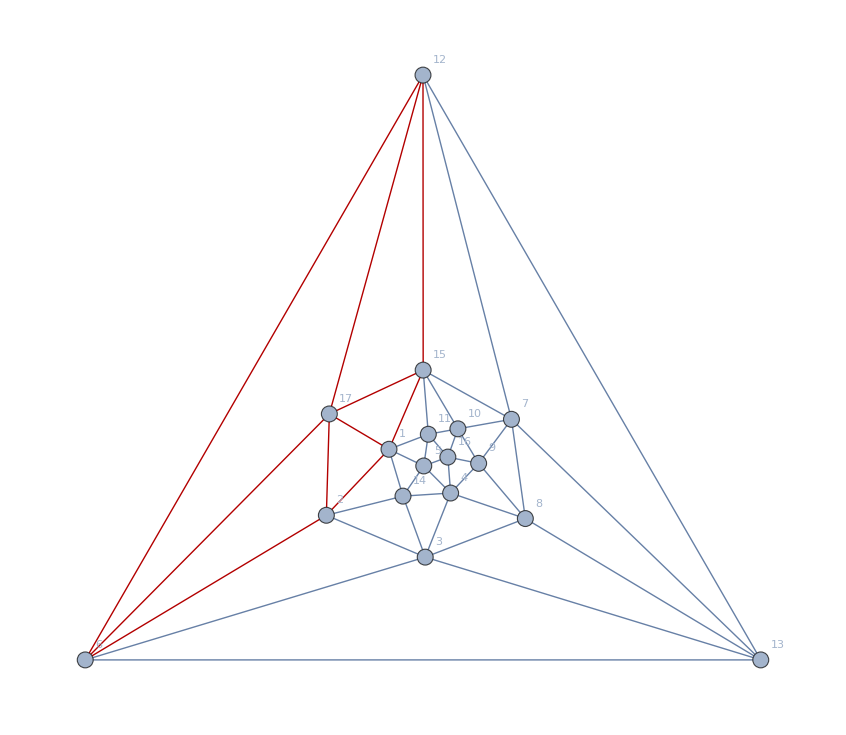

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[left]]
```

```mathematica
GetIdFromGraph[middle]
```

4862713

```mathematica
allGraphs6[4862713,"graph"]
```

-Graphics-

```mathematica
allGraphs6[4862713,"colofour"]/.RepGraph6["C"]
```

-Graphics-8952565+-Graphics-8775337+-Graphics-8946004+-Graphics-8770963+-Graphics-7358161+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7351600+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453

```mathematica
EmbedGraph6[master_,key_,vertices_]:=Block[
{val=allGraphs6[key], sets, reference=vertices, g, sub, edge,added,edges},
sets=val["vertexsets"];
g=master;
(* delete existing edges *)
Table[
Table[
edge=vertices[[i]]<->vertices[[j]];
If[EdgeQ[g,edge],
g = EdgeDelete[g,edge]
]
,{j,i+1,6}
]
,{i,1,6}
];
(* contract vertices if needed *)
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];

sub=val["graph"];
(* add edges *)
edges=Table[
reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]],
{e,EdgeList[sub]}
];
g=EdgeAdd[g,edges];
Graph[EdgeList[g],GraphLayout->"LayeredDigraphEmbedding",GraphHighlight->edges, VertexLabels->"Name"]
]
```

```mathematica
EmbedGraph6[master_,s_]:=Block[
{sets, reference, g,  edge,added,edges,vertices=Association[],less={}},
sets=SymbolToSets[s];
reference=Flatten[sets];
Table[vertices[v]=v,{v,VertexList[master]}];
g=master;
(* delete existing edges *)
Table[
Table[
edge=reference[[i]]<->reference[[j]];
If[EdgeQ[g,edge],
g = EdgeDelete[g,edge]
]
,{j,i+1,Length[reference]}
]
,{i,1,Length[reference]}
];
(* contract vertices if needed *)
Table[
AppendTo[less,First[s]];
If[Length[s]>1,
vertices[First[s]]=ToString[s];
g=VertexContract[g,s];
vertices=KeyDrop[vertices,Rest[s]];
], {s,sets}];
(* add edges *)
edges=Table[
e[[1]]<->e[[2]],
{e,Subsets[less,{2}]}
];
g=EdgeAdd[g,edges];
Graph[Keys[vertices],EdgeList[g],GraphLayout->"SpringElectricalEmbedding",GraphHighlight->edges, VertexLabels->Sort[Normal[vertices]],ImageSize->600]
]
```

```mathematica
FindFullFormula4[middle]
```

{v16x2fxcxh,v1x2fx6cxh,v16x2cxfxh,v1x2cx6fxh,v16cx2xfxh,v1cx2x6fxh,v1cx2fx6xh}

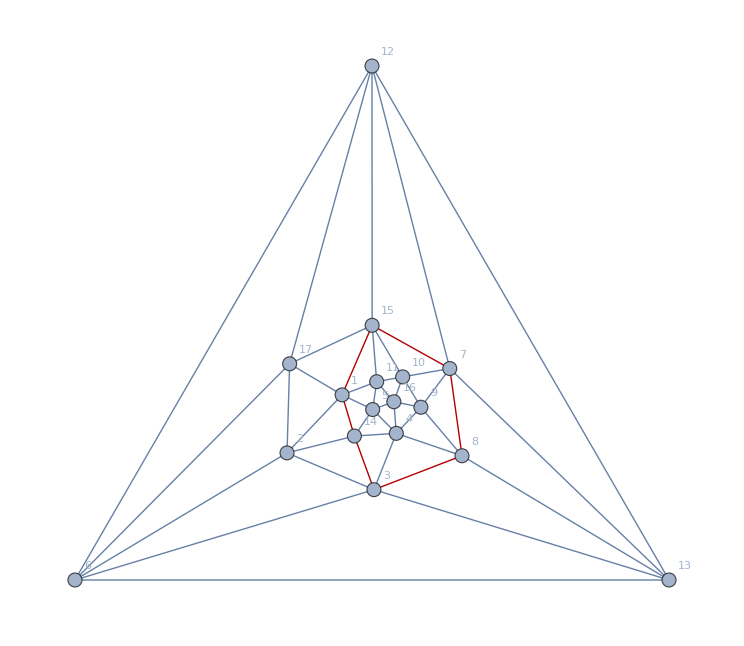

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[middle2]]
```

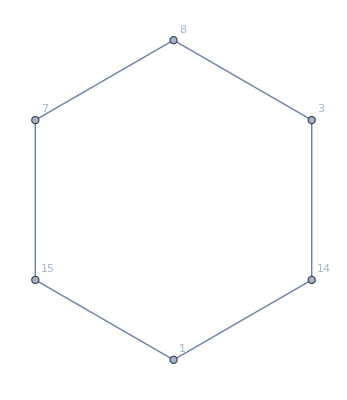

```mathematica
middle2=Subgraph[plantri8,{7,15,1,14,3,8},VertexLabels->"Name"]
```

```mathematica
FindFullFormula[middle2]
```

{v1x3x7x8xexf,v1x3x7x8exf,v18x3x7xexf,v13x7x8xexf,v13x7x8exf,v1x3x7x8fxe,v13x7x8fxe,v1x3fx7x8xe,v1x3fx7x8e,v18x3fx7xe,v1x3x7x8xef,v1x3x7x8ef,v18x3x7xef,v13x7x8xef,v13x7x8ef,v1x37x8xexf,v1x37x8exf,v18x37xexf,v1x37x8fxe,v1x37x8xef,v1x37x8ef,v18x37xef,v1x3x7ex8xf,v18x3x7exf,v13x7ex8xf,v1x3x7ex8f,v13x7ex8f,v1x3fx7ex8,v18x3fx7e,v17x3x8xexf,v137x8xexf,v17x3x8exf,v137x8exf,v17x3x8fxe,v137x8fxe,v17x3fx8xe,v17x3fx8e,v17x3x8xef,v17x3x8ef,v137x8xef,v137x8ef}

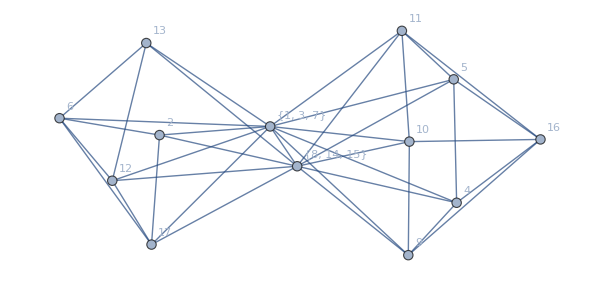
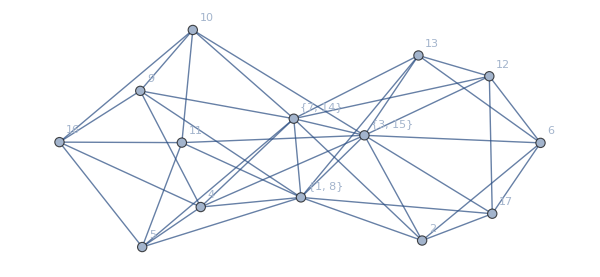
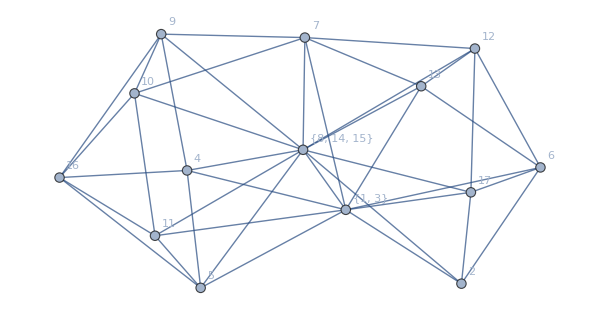
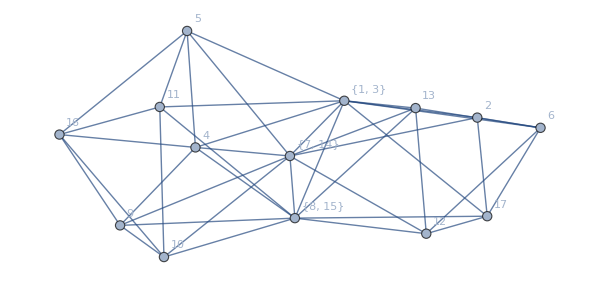
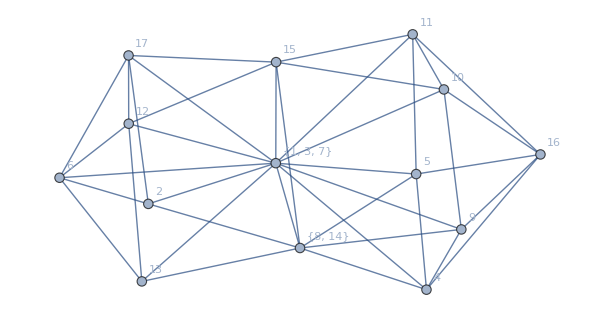
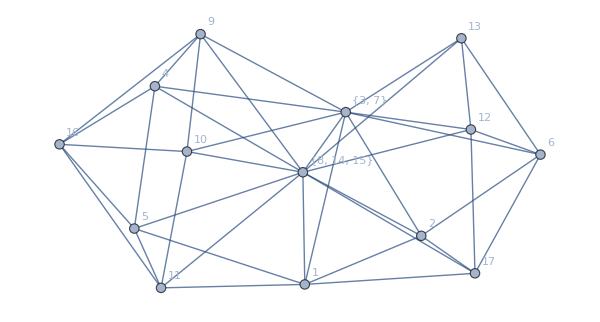
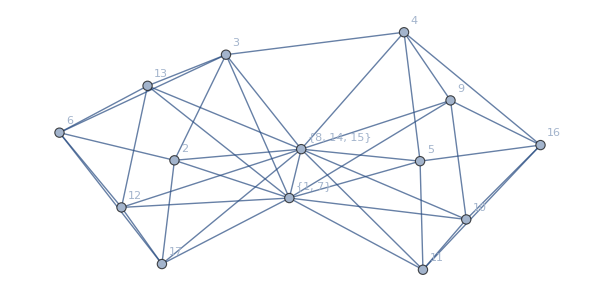
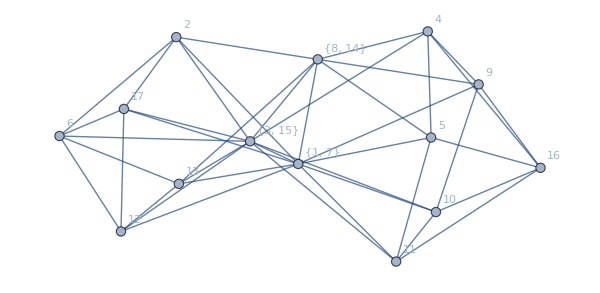
-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False+-Graphics-False

```mathematica
Map[With[{g=EmbedGraph6[plantri8,#]},Labeled[g,PlanarGraphQ[g]]]&,FindFullFormula[middle2]]//Total
```

```mathematica
Map[ChromaticPolynomial[EmbedGraph6[plantri8,#],x]&,FindFullFormula[middle2]]//Total
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

```mathematica
ChromaticPolynomial[plantri8,x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17

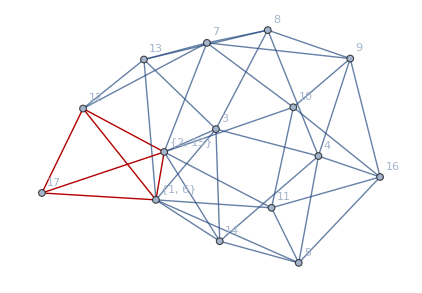

```mathematica
EmbedGraph6[plantri8,v16x2fxcxh]
```

```mathematica
ApplyMiddle[g_]:=Block[{vertices, id,h,fulls},
id=GetIdFromGraph[middle];
fulls=(ListofVars[allGraphs6[id,"colofour"]]/.RepKey6["C"]);
vertices=VertexList[middle];
Table[
h=EmbedGraph6[g,fullId,vertices];
h
,
{fullId,fulls}
]
]
```

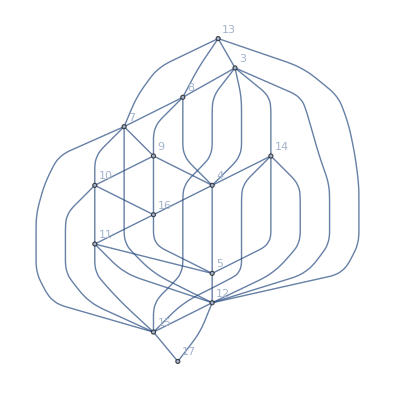
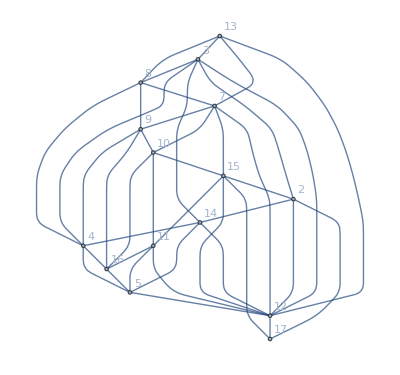
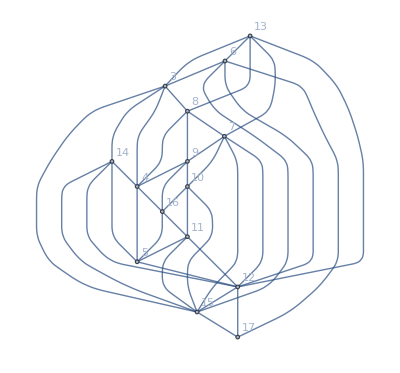
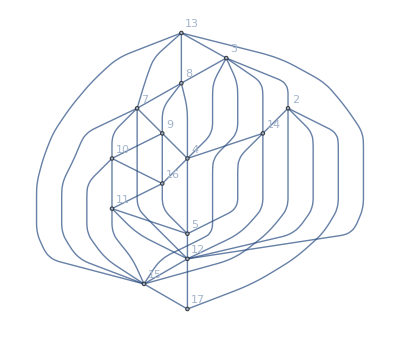
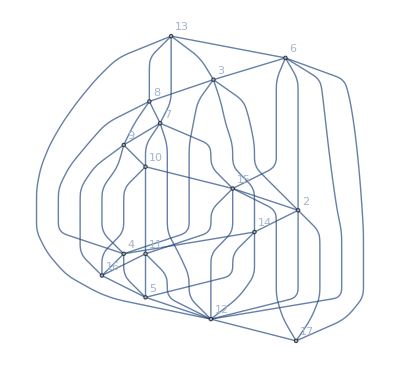
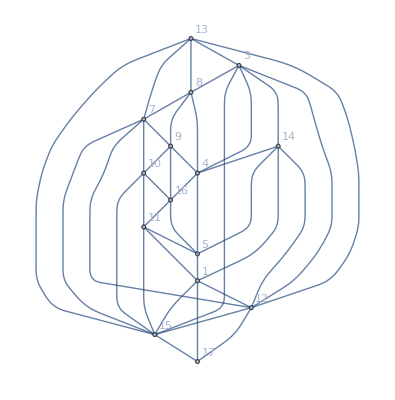
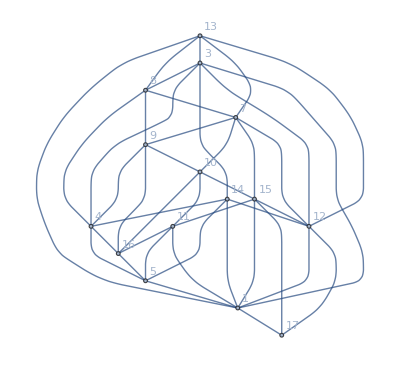
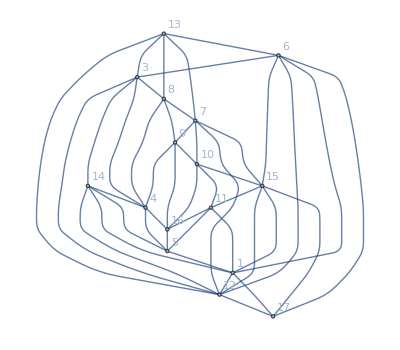
{-Graphics--Graphics-8952565GreaterEqual,-Graphics--Graphics-8946004GreaterEqual,-Graphics--Graphics-8775337GreaterEqual,-Graphics--Graphics-8770963GreaterEqual,-Graphics--Graphics-8768776Equal,-Graphics--Graphics-7708081GreaterEqual,-Graphics--Graphics-7705975GreaterEqual,-Graphics--Graphics-7705894Equal,-Graphics--Graphics-7358161GreaterEqual,-Graphics--Graphics-7351600Equal,-Graphics--Graphics-7181095GreaterEqual,-Graphics--Graphics-7181014Equal,-Graphics--Graphics-7176640Equal,-Graphics--Graphics-7174534Equal,-Graphics--Graphics-7174453Equal}

```mathematica
ApplyMiddle[plantri8]
```

```mathematica
ApplyMiddle[right]
```

{-Graphics--Graphics-8952565GreaterEqual,-Graphics--Graphics-8946004GreaterEqual,-Graphics--Graphics-8775337GreaterEqual,-Graphics--Graphics-8770963GreaterEqual,-Graphics--Graphics-8768776Equal,-Graphics--Graphics-7708081GreaterEqual,-Graphics--Graphics-7705975GreaterEqual,-Graphics--Graphics-7705894Equal,-Graphics--Graphics-7358161GreaterEqual,-Graphics--Graphics-7351600Equal,-Graphics--Graphics-7181095GreaterEqual,-Graphics--Graphics-7181014Equal,-Graphics--Graphics-7176640Equal,-Graphics--Graphics-7174534Equal,-Graphics--Graphics-7174453Equal}

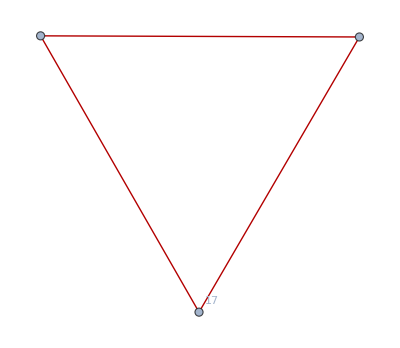
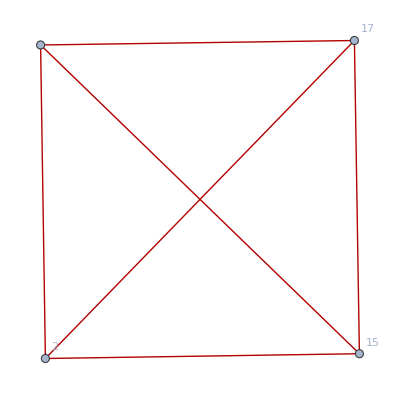
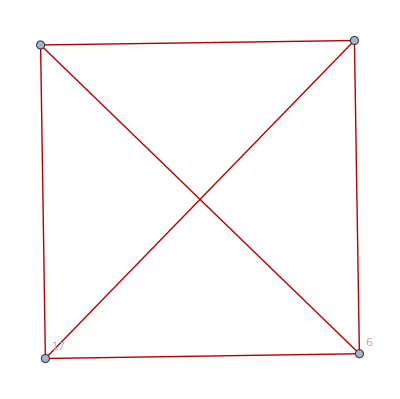
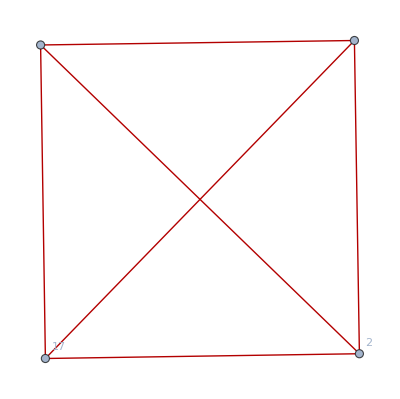
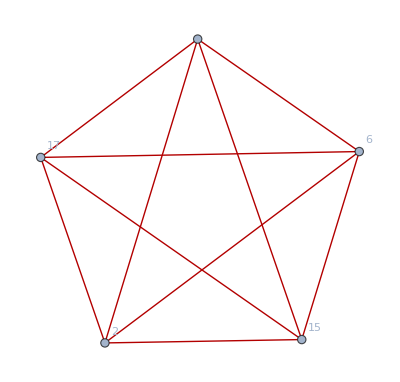
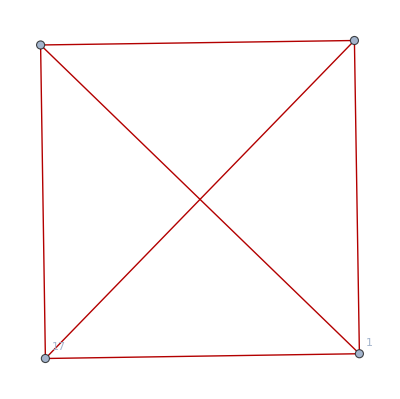
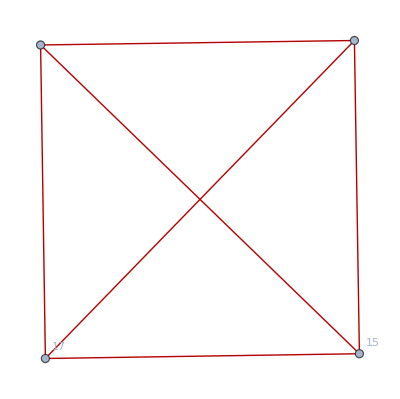
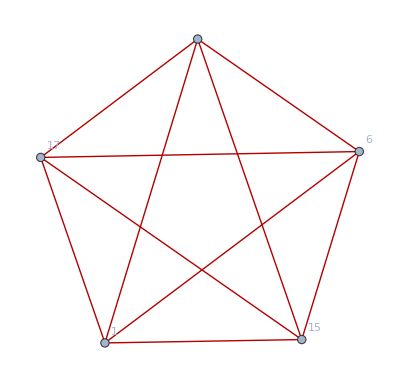
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ApplyMiddle[left]
```

```mathematica
ApplyMiddle[middle]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[RepGraph6b];RepGraph6b[base_]:=RepGraph6b[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->allGraphs6[key,"graph"],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Block[{l=ApplyMiddle[left],r=ApplyMiddle[right],id,m,i},
id=GetIdFromGraph[middle];
m=(ListofVars[allGraphs6[id,"colofour"]]/.RepGraph6b["C"]);Print[m];
Table[Expand[Simplify[(ChromaticPolynomial[l[[i]],x]*ChromaticPolynomial[r[[i]],x])/ChromaticPolynomial[m[[i]],x]]],{i,Length[m]}]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-1514304 x+6769308 x^2-13610652 x^3+16436027 x^4-13394088 x^5+7826133 x^6-3390970 x^7+1108016 x^8-273969 x^9+50751 x^10-6856 x^11+640 x^12-37 x^13+x^14,5610384 x-25900056 x^2+54402936 x^3-69523486 x^4+60796617 x^5-38690557 x^6+18556711 x^7-6836052 x^8+1948195 x^9-428054 x^10+71429 x^11-8779 x^12+751 x^13-40 x^14+x^15,8439084 x-38177130 x^2+78333362 x^3-97509118 x^4+82851749 x^5-51125224 x^6+23738512 x^7-8457473 x^8+2330120 x^9-495059 x^10+79949 x^11-9523 x^12+791 x^13-41 x^14+x^15,8158716 x-36955110 x^2+75942908 x^3-94710408 x^4+80654776 x^5-49902173 x^6+23242087 x^7-8309207 x^8+2297752 x^9-490020 x^10+79418 x^11-9489 x^12+790 x^13-41 x^14+x^15,-39599952 x+184303820 x^2-391991926 x^3+510062566 x^4-457290126 x^5+300866974 x^6-150718380 x^7+58728953 x^8-17988572 x^9+4337466 x^10-817209 x^11+118165 x^12-12690 x^13+955 x^14-45 x^15+x^16,7983738 x-36085563 x^2+74030037 x^3-92238315 x^4+78556000 x^5-48664146 x^6+22719869 x^7-8149946 x^8+2262788 x^9-484615 x^10+78858 x^11-9454 x^12+789 x^13-41 x^14+x^15,8072316 x-36428880 x^2+74610629 x^3-92807542 x^4+78916282 x^5-48818473 x^6+22765257 x^7-8159002 x^8+2263961 x^9-484704 x^10+78861 x^11-9454 x^12+789 x^13-41 x^14+x^15,-38900040 x+180650654 x^2-383470895 x^3+498261323 x^4-446422929 x^5+293816090 x^6-147391481 x^7+57569691 x^8-17689455 x^9+4280882 x^10-809564 x^11+117465 x^12-12651 x^13+954 x^14-45 x^15+x^16,6025734 x-27650265 x^2+57690913 x^3-73200493 x^4+63544391 x^5-40145747 x^6+19119918 x^7-6997300 x^8+1982199 x^9-433214 x^10+71964 x^11-8813 x^12+752 x^13-40 x^14+x^15,-28372824 x+134005578 x^2-289698433 x^3+383713569 x^4-350696114 x^5+235577985 x^6-120674161 x^7+48150922 x^8-15120218 x^9+3740655 x^10-723342 x^11+107338 x^12-11824 x^13+912 x^14-44 x^15+x^16,8087094 x-36655101 x^2+75384789 x^3-94096782 x^4+80209484 x^5-49677491 x^6+23161480 x^7-8288617 x^8+2294079 x^9-489584 x^10+79387 x^11-9488 x^12+790 x^13-41 x^14+x^15,-38959152 x+181570316 x^2-386793756 x^3+504192443 x^4-452884977 x^5+298545364 x^6-149835391 x^7+58484374 x^8-17939542 x^9+4330520 x^10-816548 x^11+118127 x^12-12689 x^13+955 x^14-45 x^15+x^16,-37837680 x+176401868 x^2-376009920 x^3+490607149 x^4-441298375 x^5+291456187 x^6-146626640 x^7+57394885 x^8-17661804 x^9+4277996 x^10-809385 x^11+117460 x^12-12651 x^13+954 x^14-45 x^15+x^16,-38191992 x+177863714 x^2-378675605 x^3+493464649 x^4-443308730 x^5+292433777 x^6-146962519 x^7+57476497 x^8-17675552 x^9+4279525 x^10-809486 x^11+117463 x^12-12651 x^13+954 x^14-45 x^15+x^16,224013840 x-1068435428 x^2+2341102052 x^3-3156700979 x^4+2952180120 x^5-2041557454 x^6+1084432188 x^7-452699114 x^8+150395728 x^9-39938311 x^10+8452140 x^11-1410157 x^12+181711 x^13-17467 x^14+1180 x^15-50 x^16+x^17}

```mathematica
Block[{l=ApplyMiddle[left],r=ApplyMiddle[right],id,m,i},
id=GetIdFromGraph[middle];
m=(ListofVars[allGraphs6[id,"colofour"]]/.RepGraph6b["C"]);
Total[Table[Simplify[ChromaticPolynomial[l[[i]],x]*ChromaticPolynomial[r[[i]],x]/ChromaticPolynomial[m[[i]],x]],{i,Length[m]}]]//Expand
]
```

53014962 x-264722275 x^2+611246439 x^3-874049397 x^4+872414080 x^5-648058755 x^6+372136480 x^7-168983373 x^8+61425710 x^9-17945766 x^10+4199616 x^11-778499 x^12+111970 x^13-12067 x^14+918 x^15-44 x^16+x^17

```mathematica
ChromaticPolynomial[plantri8,x]
```

71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17